```mathematica
mainAssoc = stubbornForm3;
```

```mathematica
PartitionToSymbol2[part_]:=Block[{end},
end=StringRiffle[Map[SetToString[#]&,Sort[part,Min[#1]<Min[#2]&]],"x"];
Symbol["p"<>end]]
```

```mathematica
GenerateAxioms2[assoc_, vertexCount_]:=Block[
{keysWith6Nodes=Select[Keys[assoc],With[{g=assoc[#]["graph"]},VertexCount[g]==vertexCount]&],
allPartitions=SetPartitions[vertexCount]},
Monitor[ 
Table[
With[
{key=First[Select[keysWith6Nodes,With[{g=assoc[#]["graph"]},IsPartitionGraph[g,part]]&]]},
mainAssoc[key,"colofour"]
]==PartitionToSymbol2[part],
{part,allPartitions}],part]
]
```

```mathematica
baseGraphAxioma3Vars//Length
```

5

```mathematica
baseGraphAxioma3Vars // Length
```

5

```mathematica
prob=GenerateAxioms2[stubbornForm3, 3];
```

```mathematica
Keys[stubbornForm3[1]]
```

{signature,matrix,graph,vertexsets,vertices,edges,relations,links,colortable,colofour,colortable2,comp,marked,parents,children,compwhy}

```mathematica
{"signature","mat3rix","graph","vertexsets","vertices","edges","relations","links","colortable","colofour","colortable2","comp","marked","parents","children","compwhy"}
```

{signature,mat3rix,graph,vertexsets,vertices,edges,relations,links,colortable,colofour,colortable2,comp,marked,parents,children,compwhy}

```mathematica
newVars=Select[Flatten[Map[ListofVars[#]&,prob]]//Sort,StringStartsQ[SymbolName[#],"p"]&]
```

{p123,p12x3,p13x2,p1x23,p1x2x3}

```mathematica
Length[newVars]
```

5

```mathematica
sol=First[Solve[prob,baseGraphAxioma3Vars]];
```

```mathematica
GetCoeff[poly_]:=CoefficientList[poly,newVars]
```

```mathematica
Map[#[[2]]&,sol]
```

{1/2 (p123-p12x3-p13x2-p1x23+2 p1x2x3),1/2 (-p123-p12x3+p13x2+p1x23),1/2 (-p123+p12x3-p13x2+p1x23),1/2 (-p123+p12x3+p13x2-p1x23),p123}

```mathematica
mat3=CoefficientArrays[Map[#[[2]]&,sol],newVars][[2]]
```

SparseArray[<18>, {5, 5}]

```mathematica
MatrixForm[mat3]
```

(1/2 | -1/2 | -1/2 | -1/2 | 1
-1/2 | -1/2 | 1/2 | 1/2 | 0
-1/2 | 1/2 | -1/2 | 1/2 | 0
-1/2 | 1/2 | 1/2 | -1/2 | 0
1 | 0 | 0 | 0 | 0)

```mathematica
MatrixForm[Inverse[mat3]]
```

(0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 1 | 1
0 | 1 | 0 | 1 | 1
0 | 1 | 1 | 0 | 1
1 | 1 | 1 | 1 | 1)

```mathematica
Map[Total[#]&,Inverse[mat3]]//Tally//Sort
```

{{1,1},{3,3},{5,1}}

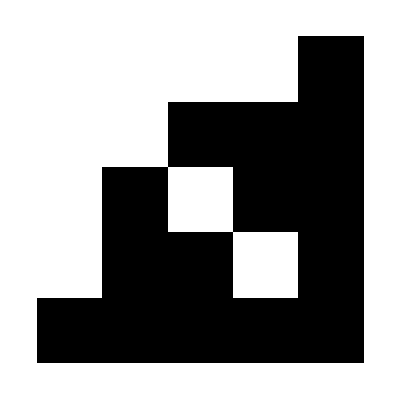

```mathematica
ArrayPlot[Inverse[mat3]]
```

```mathematica
Det[mat3]
```

-1/2

```mathematica
CharacteristicPolynomial[mat3,x]*2//Simplify
```

-(1+x)^3 (1-4 x+2 x^2)


Chromat3icPolynomial[-Graphics-,x]

```mathematica
ChromaticPolynomial[CompleteGraph[3],x]
```

```mathematica
Tr[Inverse[mat3]]
```

1